```mathematica
Clear[g1]
g1[n_,k_] := g1[n,k]=Sum[ LCM[a,b]g1[Floor[n/(a b)],k-1],{a,1,n},{b,1,n/a}]
g1[n_,0]:=UnitStep[n-1]
g2[n_,k_] := Sum[ (-1)^(k-j) Binomial[k,j] g1[n,j],{j,0,k}]
lg[n_] := Sum[ (-1)^(k+1)/k g2[n,k],{k,1,Log2@n}]
kk[n_]:=kk[n]=FullSimplify[MangoldtLambda[n]/Log[n]]
pr[n_,s_] :=Sum[ kk[j] j^s,{j,2,n}]
ts[n_] := 2pr[n,1]
ts2[n_] := 2pr[n,1]+pr[Floor[n^(1/2)],1]-pr[Floor[n^(1/2)],2]
```

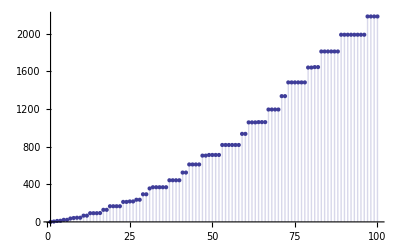

```mathematica
DiscretePlot[ lg[n],{n,1,100}]
```

```mathematica
Table[{n, lg[2^n]-lg[2^n-1], lg[3^n]-lg[3^n-1], lg[5^n]-lg[5^n-1], lg[7^n]-lg[7^n-1]},{n,1,5}]//TableForm
```

1 | 4 | 6 | 10 | 14
2 | 2 | 3 | 5 | 7
3 | 16/3 | 18 | 250/3 | 686/3
4 | 2 | 9/2 | 25/2 | 49/2
5 | 64/5 | 486/5 | 1250 | 33614/5

```mathematica
2 5^3/3
```

250/3

```mathematica
2 7^3/3
```

686/3

```mathematica
2 3^3/3
```

18

```mathematica
2 2^3/3
```

16/3

```mathematica
2 7^5/5
```

33614/5

```mathematica
2 5^5/5
```

1250

```mathematica
Table[{n, lg[2^n]-lg[2^n-1]-2 2^n kk[2^n], lg[3^n]-lg[3^n-1]-2 3^n kk[3^n]},{n,1,8}]//TableForm
```

1 | 0 | 0
2 | -2 | -6
3 | 0 | 0
4 | -6 | -36
5 | 0 | 0
6 | -56/3 | -234
7 | 0 | 0
8 | -60 | -1620

```mathematica
2 3^7/7
```

4374/7

```mathematica
2 2^7/7
```

256/7

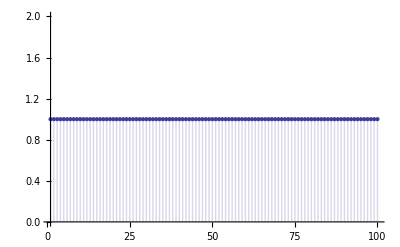

```mathematica
DiscretePlot[ lg[n]-ts2[n] + 1,{n,1,100}]
```

```mathematica
Table[ 2 kk[2^k] 2^k,{k,1,6}]
```

{4,4,16/3,8,64/5,64/3}

```mathematica
2, 12, 56, 240
```

```mathematica
6,72, 702,6480
```

```mathematica
1 2, 3 4, 7 8, 15 16
```

```mathematica
2 3, 8 9, 26 27, 80 81
```

```mathematica
2^2-2, 4^2-4, 8^2-8, 16^2-16
```

```mathematica
3^2-3, 9^2-9, 27^2-27,81^2-81
```

```mathematica
Clear[g1]
g1[n_,k_] := g1[n,k]=Sum[ LCM[a,b,c]g1[Floor[n/(a b c)],k-1],{a,1,n},{b,1,n/a}, {c,1,n/(a b)}]
g1[n_,0]:=UnitStep[n-1]
g2[n_,k_] := Sum[ (-1)^(k-j) Binomial[k,j] g1[n,j],{j,0,k}]
lg[n_] := Sum[ (-1)^(k+1)/k g2[n,k],{k,1,Log2@n}]
kk[n_]:=kk[n]=FullSimplify[MangoldtLambda[n]/Log[n]]
pr[n_,s_] :=Sum[ kk[j] j^s,{j,2,n}]
ts[n_] := 3pr[n,1]+pr[n^(1/3),1]-pr[n^(1/3),2]
```

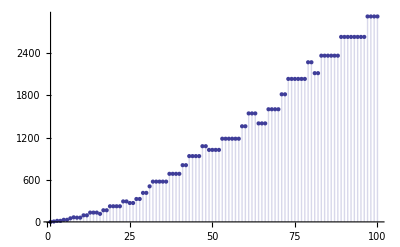

```mathematica
DiscretePlot[lg[n],{n,1,100}]
```

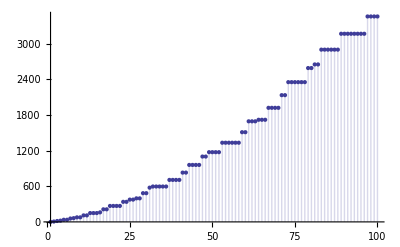

```mathematica
DiscretePlot[ts[n],{n,1,100}]
```